# MTH1030 A2

## Rui Qin

30874157

## 1. Funny numbers

### A. Show that:

#### i) the identity matrix is a funny number

```mathematica
MatrixForm[mat = {{a,-b},{b,a}}]
```

(a | -b
b | a)

The identity matrix of it is

```mathematica
MatrixForm[identitymat = {{1,0},{0,1}}]
```

(1 | 0
0 | 1)

Which meets requirement

#### ii) sums and products of funny numbers are funny numbers

sum of matrix

```mathematica
MatrixForm[mat+mat]
```

(2 a | -2 b
2 b | 2 a)

product of matrix

```mathematica
MatrixForm[mat.mat]
```

(a^2-b^2 | -2 a b
2 a b | a^2-b^2)

they all meet the funny number requirement

#### iii) all funny numbers except for one

making inverse of mat

```mathematica
MatrixForm[Inverse[mat]]
```

(a/(a^2+b^2) | b/(a^2+b^2)
-b/(a^2+b^2) | a/(a^2+b^2))

we notice each of value in matrix they all divided by a^2+b^2
that means if a=0 and b=0, the funny numbers is not valid

#### iv) multiplication of funny numbers is commutative

We make two value and multi them and check the result

```mathematica
MatrixForm[A = {{a,-b},{b,a}}];
MatrixForm[B = {{c,-d},{d,c}}]
```

(a | -b
b | a)

(c | -d
d | c)

```mathematica
MatrixForm[A.B]==MatrixForm[B.A]
```

True

The return is true which mean it meets the requirement

### B. What is the solution of the following system of two linear equations with funny number coefficients in the funny number unknowns X and Y ?

First we set up X and Y

```mathematica
X = {{x,-y},{y,x}}
Y = {{v,-w},{w,v}}
```

{{x,-y},{y,x}}

{{v,-w},{w,v}}

Then we set up the equation and let Mathematica calculate it

```mathematica
MatrixForm[{{1,0},{0,1}}.X]+MatrixForm[{{0,1},{-1,0}}.Y]==MatrixForm[{{2,0},{0,2}}]
MatrixForm[{{1,1},{-1,1}}.X]+MatrixForm[{{1,0},{0,1}}.Y]==MatrixForm[{{1,0},{0,1}}]
```

(w | v
-v | w)+(x | -y
y | x)==(2 | 0
0 | 2)

(v | -w
w | v)+(x+y | x-y
-x+y | x+y)==(1 | 0
0 | 1)

Using Solve function to solve it

```mathematica
Solve[w+x ==2&&v-y==0&&v+x+y==1&&w-x+y==0,{x,y,v,w}]
```

{{x→1,y→0,v→0,w→1}}

### C. Find the funny funny number I and inverse

#### i) Find the funny funny number plays the role of the number 1

```mathematica
mat2 = MatrixForm[{{{{a,b},{-b,a}},{{c,d},{-d,c}}},{{{-c,d},{-d,-c}},{{a,-b},{b,a}}}}]
```

((a | b
-b | a) | (c | d
-d | c)
(-c | d
-d | -c) | (a | -b
b | a))

As everyone know the identify matrix can play role of 1, let make up a matrix and try does it work

```mathematica
identifyMat2 = MatrixForm[{{{{1,0},{0,1}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{1,0},{0,1}}}}]
```

((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1))

```mathematica
mat2.identifyMat2
```

((a | b
-b | a) | (c | d
-d | c)
(-c | d
-d | -c) | (a | -b
b | a)).((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1))

We create a formula with Mathematica

Formula

```mathematica
MatrixForm[{{a,b},{c,d}}].MatrixForm[{{x,y},{m,n}}]==MatrixForm[{{a,b},{c,d}}.{{x,y},{m,n}}]
```

(a | b
c | d).(x | y
m | n)==(b m+a x | b n+a y
d m+c x | d n+c y)

Then we calculate base on it

The top left:

```mathematica
theTopLeft = MatrixForm[{{a,b},{-b,a}}.{{1,0},{0,1}}+{{c,d},{-d,c}}.{{0,0},{0,0}}]
```

(a | b
-b | a)

The top right:

```mathematica
theTopRight = MatrixForm[{{c,d},{-d,c}}.{{1,0},{0,1}}+{{a,b},{-b,a}}.{{0,0},{0,0}}]
```

(c | d
-d | c)

The bottom left:

```mathematica
theBottomLeft = MatrixForm[{{-c,d},{-d,-c}}.{{1,0},{0,1}}+{{a,b},{-b,a}}.{{0,0},{0,0}}]
```

(-c | d
-d | -c)

The bottom right:

```mathematica
theBottomRight = MatrixForm[{{a,-b},{b,a}}.{{1,0},{0,1}}+{{-c,d},{-d,-c}}.{{0,0},{0,0}}]
```

(a | -b
b | a)

Result:

```mathematica
MatrixForm[{{theTopLeft,theTopRight},{theBottomLeft,theBottomRight}}]==mat2
```

((a | b
-b | a) | (c | d
-d | c)
(-c | d
-d | -c) | (a | -b
b | a))==((a | b
-b | a) | (c | d
-d | c)
(-c | d
-d | -c) | (a | -b
b | a))

which is same as mat2, that means identifyMat2 meets the property that IF = F I = F

#### ii) Which funny funny numbers have an inverse?

Firstly set up a matrix called mat3 as the inverse of mat2

```mathematica
mat2
mat3 = MatrixForm[{{{{x,y},{-y,x}},{{m,n},{-n,m}}},{{{-m,n},{-n,-m}},{{x,-y},{y,x}}}}]
```

((a | b
-b | a) | (c | d
-d | c)
(-c | d
-d | -c) | (a | -b
b | a))

((x | y
-y | x) | (m | n
-n | m)
(-m | n
-n | -m) | (x | -y
y | x))

Then we multi them

mat2*mat3

The top left:

```mathematica
topleft=MatrixForm[({{a, b}, {-b, a}}).({{x, y}, {-y, x}})+({{-c, d}, {-d, -c}}).({{m, n}, {-n, m}})]
```

(-c m-d n+a x-b y | d m-c n+b x+a y
-d m+c n-b x-a y | -c m-d n+a x-b y)

The top right:

```mathematica
topright=MatrixForm[({{c, d}, {-d, c}}).({{x, y}, {-y, x}})+({{a, -b}, {b, a}}).({{m, n}, {-n, m}})]
```

(a m+b n+c x-d y | -b m+a n+d x+c y
b m-a n-d x-c y | a m+b n+c x-d y)

The bottom left:

```mathematica
bottomleft = MatrixForm[({{a, b}, {-b, a}}).({{-m, n}, {-n, -m}})+({{-c, d}, {-d, -c}}).({{x, -y}, {y, x}})]
```

(-a m-b n-c x+d y | -b m+a n+d x+c y
b m-a n-d x-c y | -a m-b n-c x+d y)

The bottom right:

```mathematica
bottomright = MatrixForm[({{c, d}, {-d, c}}).({{-m, n}, {-n, -m}})+({{a, -b}, {b, a}}).({{x, -y}, {y, x}})]
```

(-c m-d n+a x-b y | -d m+c n-b x-a y
d m-c n+b x+a y | -c m-d n+a x-b y)

Result:

```mathematica
MatrixForm[{{topleft,topright},{bottomleft,bottomright}}]
```

((-c m-d n+a x-b y | d m-c n+b x+a y
-d m+c n-b x-a y | -c m-d n+a x-b y) | (a m+b n+c x-d y | -b m+a n+d x+c y
b m-a n-d x-c y | a m+b n+c x-d y)
(-a m-b n-c x+d y | -b m+a n+d x+c y
b m-a n-d x-c y | -a m-b n-c x+d y) | (-c m-d n+a x-b y | -d m+c n-b x-a y
d m-c n+b x+a y | -c m-d n+a x-b y))

The result is equal to the inverse of mat2. So:

```mathematica
-c m-d n+a x-b y==1
b m-a n-d x-c y == 0
a m+b n+c x-d y ==0
d m-c n+b x+a y==0
```

```mathematica
Solve[-c m-d n+a x-b y==1&&b m-a n-d x-c y == 0&&a m+b n+c x-d y ==0&&d m-c n+b x+a y==0,{m,n,x,y}]
```

{{m→-c/(a^2+b^2+c^2+d^2),n→-d/(a^2+b^2+c^2+d^2),x→a/(a^2+b^2+c^2+d^2),y→-b/(a^2+b^2+c^2+d^2)}}

We notice: in this case, a^2+b^2+c^2+d^2 cannot be 0, then the funny funny number has inverse

### D. Find two funny funny numbers A and B such that AB != BA

We replace the a and x with 0

```mathematica
mat2 = MatrixForm[{{{{0,b},{-b,0}},{{c,d},{-d,c}}},{{{-c,d},{-d,-c}},{{0,-b},{b,0}}}}]
```

((0 | b
-b | 0) | (c | d
-d | c)
(-c | d
-d | -c) | (0 | -b
b | 0))

```mathematica
mat3 = MatrixForm[{{{{0,y},{-y,0}},{{m,n},{-n,m}}},{{{-m,n},{-n,-m}},{{0,-y},{y,0}}}}]
```

((0 | y
-y | 0) | (m | n
-n | m)
(-m | n
-n | -m) | (0 | -y
y | 0))

and we multi mat2 and mat3

```mathematica
MatrixForm[({{({{0, b}, {-b, 0}}), ({{c, d}, {-d, c}})}, {({{-c, d}, {-d, -c}}), ({{0, -b}, {b, 0}})}}).({{({{0, y}, {-y, 0}}), ({{m, n}, {-n, m}})}, {({{-m, n}, {-n, -m}}), ({{0, -y}, {y, 0}})}})]
```

(((-b m | b n
-b n | -b m) | (0 | -b y
b y | 0)
(0 | -b y
b y | 0) | (-b m | -b n
b n | -b m)) | ((-d m | d n+c y
-d n-c y | -d m) | (c m | c n-d y
-c n+d y | c m)
(-c m | c n-d y
-c n+d y | -c m) | (-d m | -d n-c y
d n+c y | -d m))
((-d m | d n-c y
-d n+c y | -d m) | (-c m | -c n-d y
c n+d y | -c m)
(c m | -c n-d y
c n+d y | c m) | (-d m | -d n+c y
d n-c y | -d m)) | ((b m | -b n
b n | b m) | (0 | b y
-b y | 0)
(0 | b y
-b y | 0) | (b m | b n
-b n | b m)))

then we switch to mat3 multi with mat2

```mathematica
MatrixForm[({{({{0, y}, {-y, 0}}), ({{m, n}, {-n, m}})}, {({{-m, n}, {-n, -m}}), ({{0, -y}, {y, 0}})}}).({{({{0, b}, {-b, 0}}), ({{c, d}, {-d, c}})}, {({{-c, d}, {-d, -c}}), ({{0, -b}, {b, 0}})}})]
```

(((-c y | d y
-d y | -c y) | (0 | -b y
b y | 0)
(0 | -b y
b y | 0) | (-c y | -d y
d y | -c y)) | ((-c n | b m+d n
-b m-d n | -c n) | (c m | d m-b n
-d m+b n | c m)
(-c m | d m-b n
-d m+b n | -c m) | (-c n | -b m-d n
b m+d n | -c n))
((-c n | -b m+d n
b m-d n | -c n) | (-c m | -d m-b n
d m+b n | -c m)
(c m | -d m-b n
d m+b n | c m) | (-c n | b m-d n
-b m+d n | -c n)) | ((c y | -d y
d y | c y) | (0 | b y
-b y | 0)
(0 | b y
-b y | 0) | (c y | d y
-d y | c y)))

We can notice there are a strong different between these two result. So AB != BA

## 2. What’s next?

### A

```mathematica
M = MatrixForm[({{a, b}, {c, d}})]
```

(a | b
c | d)

Set x(n-1) = x_(n-1), x(n-2) = x_(n-2)

```mathematica
MwithX=MatrixForm[({{a, b}, {c, d}}).({{Subscript[x, n-1]}, {Subscript[x, n-2]}})]
```

(b x_(-2+n)+a x_(-1+n)
d x_(-2+n)+c x_(-1+n))

Then we get:

```mathematica
M = MatrixForm[({{5, -6}, {1, 0}})];
```

### B

{{5,-6},{1,0}}

WolframAlphaQueryResults

```mathematica
S = ({{2, 3}, {1, 1}});
J = ({{2, 0}, {0, 3}});
S = {{-1, 3}, {1, -2}};
```

Eigenvalues:
λ_1=3
λ_2=2

Eigenvectors:

```mathematica
Subscript[v, 1]==""(,","31)"";
Subscript[v, 2]==""(,","21)"";
```

### C

```mathematica
MatrixForm[S.MatrixPower[J,n].Inverse[S].Transpose[{{1,0}}]]
```

(-2^(1+n)+3^(1+n)
-2^n+3^n)

Result:

```mathematica
f[n_] =-2^n+3^n
```

-2^n+3^n

```mathematica
N[f[2]]
N[f[3]]
N[f[4]]
```

5.

19.

65.

## 3. Matrices of Graphs

### A. The trace of a matrix, tr(A), is the sum of all the entries on the main diagonal. Explain

#### 1) tr(A) = 0

In A, point to point itself with one step no need to depend on other points, and they cannot go to other point and come back, that will be 2 steps. So in the diagonal of matrix, all the numbers are 0, so the sum of them are 0

#### 2) tr(A^2) = 2 × the number of edges of the graph

```mathematica
MatrixForm[({{0, 1, 0, 1}, {1, 0, 2, 1}, {0, 2, 0, 0}, {1, 1, 0, 0}}).({{0, 1, 0, 1}, {1, 0, 2, 1}, {0, 2, 0, 0}, {1, 1, 0, 0}})]
```

(2 | 1 | 2 | 1
1 | 6 | 0 | 1
2 | 0 | 4 | 2
1 | 1 | 2 | 2)

In A^2, two points and one edge can make a line. We set up point A and point B and they have relationship
-Graphics-
Each time we count the paths of point to point itself, the action always from point itself to other point and then from other point back to itself. Therefore, the count of A^2 it actually counting the number of edge. 

Then we notice point A on edge AB, also B on edge AB too. The B to B itself also have to go though edge AB again, which means the edge AB will be counted twice.

Therefore, The trace of A^2 is 2 * number of edges of the graph

#### 3) tr(A^3) = 6×the number of triangles in the graph

```mathematica
MatrixForm[({{0, 1, 0, 1}, {1, 0, 2, 1}, {0, 2, 0, 0}, {1, 1, 0, 0}}).({{0, 1, 0, 1}, {1, 0, 2, 1}, {0, 2, 0, 0}, {1, 1, 0, 0}}).({{0, 1, 0, 1}, {1, 0, 2, 1}, {0, 2, 0, 0}, {1, 1, 0, 0}})]
```

(2 | 7 | 2 | 3
7 | 2 | 12 | 7
2 | 12 | 0 | 2
3 | 7 | 2 | 2)

We start with focus on one point. The path should go though 3 edges and back on itself, so this path always creates a triangle.

While drawing a triangle, we can in clockwise order and counter clockwise order. 
-Graphics-
That means each one triangle can be count twice time, while we just focus on one point.

A triangle is form by three points. That means the triangle will be counted 3 times while we calculate the trace
Therefore, tr(A^3) = 2×3×the number of triangles in the graph = 6×the number of triangles in the graph

### B. Show that a graph cannot be two-coloured if the trace of any of the odd powers of A differs from 0

We firstly set up the even power: A^4 in a square. And all initial colour are set as while, other colour set as red. 
-Graphics-
we can notice that A cannot connect with both red edges.
Due to we have to change color if we already draw a  line, I would like to group a white line and a red line as a group.
So while tr(A^(2n)) is not 0, that means there are no groups are separate into individual white line or red line.
-Graphics-
While tr(A^(2n+1)) is not 0, that means there are a groups are separate into individual white line or red line but it still can finish the point line to itself. 

We can notice that whatever it is odd or even, it is always the start line(the line goes out from the point) and the back line(the line come back into the point) can decide if colour of lines are same, and the colour start line is always white.

Therefore, the red line always represent the even, and white line is always odd. When start with a point and go though odd times, it can back to the point itself, the back line is always white.

We can also using Mathematica to prove A is two-colourable

```mathematica
origin = ({{0, 1, 0, 1}, {1, 0, 2, 1}, {0, 2, 0, 0}, {1, 1, 0, 0}});
```

```mathematica
Tr[MatrixPower[origin,(2n-1)]]
```

-1/2 (-1)^(2 n)+1/2 (-1)^(1+2 n)+((-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035) (Root0.642Root[4-6 #1-#1^2+#1^3&,2]0.6420736324815003)^(-1+2 n) Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977)/(-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977+Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)+((Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524) (Root-2.32Root[4-6 #1-#1^2+#1^3&,1]-2.3234042760864777)^(-1+2 n) Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777)/(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)+(Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 (Root2.68Root[4-6 #1-#1^2+#1^3&,3]2.6813306436049773)^(-1+2 n) (-Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977))/(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)+((Root2.68Root[4-6 #1-#1^2+#1^3&,3]2.6813306436049773)^(-1+2 n) (Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977))/(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)+(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 (Root0.642Root[4-6 #1-#1^2+#1^3&,2]0.6420736324815003)^(-1+2 n) (Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773))/(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)+((-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035) (Root2.68Root[4-6 #1-#1^2+#1^3&,3]2.6813306436049773)^(-1+2 n) Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)/(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)+(Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 (Root-2.32Root[4-6 #1-#1^2+#1^3&,1]-2.3234042760864777)^(-1+2 n) (-Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977+Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773))/(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)+((Root-2.32Root[4-6 #1-#1^2+#1^3&,1]-2.3234042760864777)^(-1+2 n) (Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773))/(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)+((Root0.642Root[4-6 #1-#1^2+#1^3&,2]0.6420736324815003)^(-1+2 n) (-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773))/(Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777-Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777+Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977-Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773+Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035 Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773)

### C.

#### i) How would you measure the distance between two given vertices and the diameter of a graph using the matrices Pm?

```mathematica
matrix = MatrixForm[origin]
```

(0 | 1 | 0 | 1
1 | 0 | 2 | 1
0 | 2 | 0 | 0
1 | 1 | 0 | 0)

```mathematica
matrix1 = MatrixForm[MatrixPower[origin,2]]
```

(2 | 1 | 2 | 1
1 | 6 | 0 | 1
2 | 0 | 4 | 2
1 | 1 | 2 | 2)

Add up

```mathematica
MatrixForm[({{0, 1, 0, 1}, {1, 0, 2, 1}, {0, 2, 0, 0}, {1, 1, 0, 0}})+({{2, 1, 2, 1}, {1, 6, 0, 1}, {2, 0, 4, 2}, {1, 1, 2, 2}})]
```

(2 | 2 | 2 | 2
2 | 6 | 2 | 2
2 | 2 | 4 | 2
2 | 2 | 2 | 2)

We notice that in here every block is full and in Pm m== 2, which means diameter is 2

#### ii) How could you decide, again using these matrices, whether or not a graph is connected or disconnected?

We can cut the diagram A into two part by breaking point 2
Then we make power of matrix with the number of points

```mathematica
MatrixForm[MatrixPower[({{0, 1, 0, 1}, {1, 0, 0, 1}, {0, 0, 0, 0}, {1, 1, 0, 0}}),4]]
```

(6 | 5 | 0 | 5
5 | 6 | 0 | 5
0 | 0 | 0 | 0
5 | 5 | 0 | 6)

We notice that there are some 0 inside of it, now we try connect 1 point 2 and point 3

```mathematica
MatrixForm[MatrixPower[({{0, 1, 0, 1}, {1, 0, 1, 1}, {0, 1, 0, 0}, {1, 1, 0, 0}}),4]]
```

(7 | 6 | 4 | 6
6 | 11 | 2 | 6
4 | 2 | 3 | 4
6 | 6 | 4 | 7)

Result: If the power of matrix with the number of points still have 0 inside of it, that means it is not connected. And in fact, whatever how large number of the power, there are still 0 inside of matrix.

```mathematica
MatrixForm[MatrixPower[({{0, 1, 0, 1}, {1, 0, 0, 1}, {0, 0, 0, 0}, {1, 1, 0, 0}}),50]]
```

(375299968947542 | 375299968947541 | 0 | 375299968947541
375299968947541 | 375299968947542 | 0 | 375299968947541
0 | 0 | 0 | 0
375299968947541 | 375299968947541 | 0 | 375299968947542)

### D. Use the results in a), b) and c) to answer the following questions

#### Initial

```mathematica
A = ({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}});
```

#### i) How many triangles does this graph have?

```mathematica
Tr[({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}}).({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}}).({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}})]
```

0

There are no triangle in the graph

#### ii) Is the graph connected?

```mathematica
MatrixForm[MatrixPower[({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}}),8]]
```

(1641 | 0 | 0 | 1640 | 0 | 1640 | 1640 | 0
0 | 1641 | 1640 | 0 | 1640 | 0 | 0 | 1640
0 | 1640 | 1641 | 0 | 1640 | 0 | 0 | 1640
1640 | 0 | 0 | 1641 | 0 | 1640 | 1640 | 0
0 | 1640 | 1640 | 0 | 1641 | 0 | 0 | 1640
1640 | 0 | 0 | 1640 | 0 | 1641 | 1640 | 0
1640 | 0 | 0 | 1640 | 0 | 1640 | 1641 | 0
0 | 1640 | 1640 | 0 | 1640 | 0 | 0 | 1641)

the graph is not connected

#### iii) What is its diameter?

We make A^2 and A^3

```mathematica
MatrixForm[MatrixPower[({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}}),2]]
 MatrixForm[MatrixPower[({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}}),3]]
```

(3 | 0 | 0 | 2 | 0 | 2 | 2 | 0
0 | 3 | 2 | 0 | 2 | 0 | 0 | 2
0 | 2 | 3 | 0 | 2 | 0 | 0 | 2
2 | 0 | 0 | 3 | 0 | 2 | 2 | 0
0 | 2 | 2 | 0 | 3 | 0 | 0 | 2
2 | 0 | 0 | 2 | 0 | 3 | 2 | 0
2 | 0 | 0 | 2 | 0 | 2 | 3 | 0
0 | 2 | 2 | 0 | 2 | 0 | 0 | 3)

(0 | 7 | 7 | 0 | 7 | 0 | 0 | 6
7 | 0 | 0 | 7 | 0 | 7 | 6 | 0
7 | 0 | 0 | 7 | 0 | 6 | 7 | 0
0 | 7 | 7 | 0 | 6 | 0 | 0 | 7
7 | 0 | 0 | 6 | 0 | 7 | 7 | 0
0 | 7 | 6 | 0 | 7 | 0 | 0 | 7
0 | 6 | 7 | 0 | 7 | 0 | 0 | 7
6 | 0 | 0 | 7 | 0 | 7 | 7 | 0)

Then we start with P2 =  A+A^2

```mathematica
MatrixForm[({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}})+({{3, 0, 0, 2, 0, 2, 2, 0}, {0, 3, 2, 0, 2, 0, 0, 2}, {0, 2, 3, 0, 2, 0, 0, 2}, {2, 0, 0, 3, 0, 2, 2, 0}, {0, 2, 2, 0, 3, 0, 0, 2}, {2, 0, 0, 2, 0, 3, 2, 0}, {2, 0, 0, 2, 0, 2, 3, 0}, {0, 2, 2, 0, 2, 0, 0, 3}})]
```

(3 | 1 | 1 | 2 | 1 | 2 | 2 | 0
1 | 3 | 2 | 1 | 2 | 1 | 0 | 2
1 | 2 | 3 | 1 | 2 | 0 | 1 | 2
2 | 1 | 1 | 3 | 0 | 2 | 2 | 1
1 | 2 | 2 | 0 | 3 | 1 | 1 | 2
2 | 1 | 0 | 2 | 1 | 3 | 2 | 1
2 | 0 | 1 | 2 | 1 | 2 | 3 | 1
0 | 2 | 2 | 1 | 2 | 1 | 1 | 3)

There are still some 0, now we try P3 = A+A^2+A^3

```mathematica
MatrixForm[({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}})+({{3, 0, 0, 2, 0, 2, 2, 0}, {0, 3, 2, 0, 2, 0, 0, 2}, {0, 2, 3, 0, 2, 0, 0, 2}, {2, 0, 0, 3, 0, 2, 2, 0}, {0, 2, 2, 0, 3, 0, 0, 2}, {2, 0, 0, 2, 0, 3, 2, 0}, {2, 0, 0, 2, 0, 2, 3, 0}, {0, 2, 2, 0, 2, 0, 0, 3}})+({{0, 7, 7, 0, 7, 0, 0, 6}, {7, 0, 0, 7, 0, 7, 6, 0}, {7, 0, 0, 7, 0, 6, 7, 0}, {0, 7, 7, 0, 6, 0, 0, 7}, {7, 0, 0, 6, 0, 7, 7, 0}, {0, 7, 6, 0, 7, 0, 0, 7}, {0, 6, 7, 0, 7, 0, 0, 7}, {6, 0, 0, 7, 0, 7, 7, 0}})]
```

(3 | 8 | 8 | 2 | 8 | 2 | 2 | 6
8 | 3 | 2 | 8 | 2 | 8 | 6 | 2
8 | 2 | 3 | 8 | 2 | 6 | 8 | 2
2 | 8 | 8 | 3 | 6 | 2 | 2 | 8
8 | 2 | 2 | 6 | 3 | 8 | 8 | 2
2 | 8 | 6 | 2 | 8 | 3 | 2 | 8
2 | 6 | 8 | 2 | 8 | 2 | 3 | 8
6 | 2 | 2 | 8 | 2 | 8 | 8 | 3)

All block is full, and m=3, So the diameter is 3

#### iv) Is it two-colourable?

```mathematica
Tr[MatrixPower[A,(2n-1)]]
```

3+1/2 (-3)^(-1+2 n)-3/4 (-1)^(2 n)+9/4 (-1)^(1+2 n)+3^(-1+2 n)-1/2 (-1)^(2 n) 3^(-1+2 n)

```mathematica
Simplify[3+1/2 (-3)^(-1+2 n)-3/4 (-1)^(2 n)+9/4 (-1)^(1+2 n)+3^(-1+2 n)-1/2 (-1)^(2 n) 3^(-1+2 n)]
```

-1/3 (-1+(-1)^(2 n)) (9+9^n)

```mathematica
∑_(n=1)^∞ -1/3 (-1+(-1)^(2 n)) (9+9^n)
```

0

No, it is can not be two colorable

### E.

#### i) What does this mean for the graph?

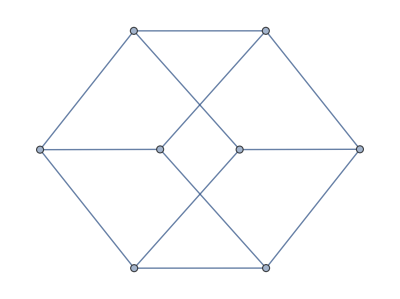

```mathematica
AdjacencyGraph[{{0,1,1,0,1,0,0,0},{1,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0},{0,1,1,0,0,0,0,1},{1,0,0,0,0,1,1,0},{0,1,0,0,1,0,0,1},{0,0,1,0,1,0,0,1},{0,0,0,1,0,1,1,0}}]
```

That mean every point only have 3 edges connect with it

{{0,1,1,0,1,0,0,0},{1,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0},{0,1,1,0,0,0,0,1},{1,0,0,0,0,1,1,0},{0,1,0,0,1,0,0,1},{0,0,1,0,1,0,0,1},{0,0,0,1,0,1,1,0}}

WolframAlphaQueryResults

We can get eigenvalues and eigenvectors in here.

Then we try put K inside of it

{{0,k,k,0,k,0,0,0},{k,0,0,k,0,k,0,0},{k,0,0,k,0,0,k,0},{0,k,k,0,0,0,0,k},{k,0,0,0,0,k,k,0},{0,k,0,0,k,0,0,k},{0,0,k,0,k,0,0,k},{0,0,0,k,0,k,k,0}}

WolframAlphaQueryResults

The eigenvalue is the {1,-1,3,-3} times of k, and their eigenvector are always the same.

### F. Geometric Series of matrices

When determinant of (I-A) is not 0, then the matrix would be valid.

```mathematica
IdentityMatrix[8]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Det[Inverse[({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}})-({{0, 1, 1, 0, 1, 0, 0, 0}, {1, 0, 0, 1, 0, 1, 0, 0}, {1, 0, 0, 1, 0, 0, 1, 0}, {0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1, 1, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 1, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 1, 1, 0}})]]
```

Inverse::sing: Matrix {{1,-1,-1,0,-1,0,0,0},{-1,1,0,-1,0,-1,0,0},{-1,0,1,-1,0,0,-1,0},{0,-1,-1,1,0,0,0,-1},{-1,0,0,0,1,-1,-1,0},{0,-1,0,0,-1,1,0,-1},{0,0,-1,0,-1,0,1,-1},{0,0,0,-1,0,-1,-1,1}} is singular.

Det[Inverse[{{1,-1,-1,0,-1,0,0,0},{-1,1,0,-1,0,-1,0,0},{-1,0,1,-1,0,0,-1,0},{0,-1,-1,1,0,0,0,-1},{-1,0,0,0,1,-1,-1,0},{0,-1,0,0,-1,1,0,-1},{0,0,-1,0,-1,0,1,-1},{0,0,0,-1,0,-1,-1,1}}]]

Crazy matrix is not work.